```mathematica
Quit[]
```

$Aborted

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

```mathematica
Quantity[3,"Minutes"]
```

3 min

```mathematica
FileSize[$CommandLine[[1]]]
```

48.304 kB

## update

```mathematica
PacletUninstall["AST"]
```

PacletUninstall::notfound: Paclet AST not found.

$Failed

```mathematica
PacletInstall["/Users/brenton/development/stash/COD/ast/build/paclet/AST-999.paclet"]
```

PacletObject[AST,999,<>]

```mathematica
PacletDirectoryAdd["/Users/brenton/development/stash/COD/ast/build/paclet/AST"];
```

```mathematica
FindFile["AST`"]
```

/Users/brenton/development/stash/COD/ast/build/paclet/AST/Kernel/AST.wl

```mathematica
PacletUpdate["AST","UpdateSites"->True]
```

PacletObject[AST,0.15,<>]

## alphasource Git error

git remote prune origin

git gc --prune=now

git remote prune origin

## build with gcc for -Weffc++ warnings

mkdir build-gcc
cd build-gcc
cmake -DWOLFRAMKERNEL=/Applications/Mathematica110.app/Contents/MacOS/WolframKernel -DCMAKE_CXX_COMPILER=/usr/local/bin/g++-8 -DCMAKE_C_COMPILER=/usr/local/bin/gcc-8 ..
cmake --build . --target paclet

## build with a compilation command database for clang-tidy

mkdir build-clang-tidy
cd build-clang-tidy
cmake -DCMAKE_EXPORT_COMPILE_COMMANDS=ON ..

generates a compile_commands.json in current directory that clang-tidy uses

clang-tidy ByteDecoder.cpp
clang-tidy ByteEncoder.cpp
...

## build for afl fuzzing

Building AFL for the kernel

# build llvm

cd llvm-development
mkdir llvm8
cd llvm8
git clone https://github.com/llvm/llvm-project.git

cd llvm-project/

git fetch
git checkout release/8.x

mkdir build

cd build

cmake -DLLVM_BUILD_LLVM_DYLIB=ON -DLLVM_LINK_LLVM_DYLIB=ON -DLLVM_ENABLE_RTTI=ON -DCMAKE_OSX_DEPLOYMENT_TARGET=10.10 -DCMAKE_INSTALL_PREFIX=install -DLLVM_ENABLE_PROJECTS="clang;libcxx;libcxxabi;lld;compiler-rt" -G "Ninja" ../llvm

ninja
ninja install

# build afl

export CC=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang
export CXX=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang++

cd afl-2.5b
CFLAGS="-mmacosx-version-min=10.10" make

cd llvm-mode
export LLVM_CONFIG=/Users/brenton/development/llvm-development/llvm801/llvm-project/build/install/bin/llvm-config
CFLAGS="-mmacosx-version-min=10.10" make

# build ast

export AFL_CC=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang
export AFL_CXX=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang++

mkdir build-afl
cd build-afl
cmake -DCMAKE_INSTALL_PREFIX=install -DBUILD_EXE=ON -DCMAKE_BUILD_TYPE=Debug -DCMAKE_C_COMPILER=/Users/brenton/development/other-development/afl-2.52b/afl-clang-fast  -DCMAKE_CXX_COMPILER=/Users/brenton/development/other-development/afl-2.52b/afl-clang-fast++ ..

cmake --build . --target ast-exe

/Users/brenton/development/other-development/afl-2.52b/afl-fuzz -i /Users/brenton/development/stash/COD/ast/Tests/files/small -o afl_out/ -x ../Tests/wl.dict cpp/src/exe/ast -n -file @@

## build for GCOV

mkdir build-gcc
cd build-gcc

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o API.o -c ../cpp/src/lib/API.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteBuffer.o -c ../cpp/src/lib/ByteBuffer.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteDecoder.o -c ../cpp/src/lib/ByteDecoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteEncoder.o -c ../cpp/src/lib/ByteEncoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CharacterDecoder.o -c ../cpp/src/lib/CharacterDecoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Node.o -c ../cpp/src/lib/Node.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Parselet.o -c ../cpp/src/lib/Parselet.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Parser.o -c ../cpp/src/lib/Parser.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Source.o -c ../cpp/src/lib/Source.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o SemiSemiParselet.o -c ../cpp/src/lib/SemiSemiParselet.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Tokenizer.o -c ../cpp/src/lib/Tokenizer.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Utils.o -c ../cpp/src/lib/Utils.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o WLCharacter.o -c ../cpp/src/lib/WLCharacter.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CharacterMaps.o -c ../build/generated/cpp/src/lib/CharacterMaps.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Token.o -c ../cpp/src/lib/Token.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CodePoint.o -c ../build/generated/cpp/src/lib/CodePoint.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Symbol.o -c ../build/generated/cpp/src/lib/Symbol.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o TokenEnum.o -c ../build/generated/cpp/src/lib/TokenEnum.cpp


/usr/local/bin/g++-8 --coverage -dynamiclib API.o ByteBuffer.o ByteDecoder.o ByteEncoder.o CharacterDecoder.o Node.o Parselet.o Parser.o SemiSemiParselet.o Source.o Tokenizer.o Utils.o WLCharacter.o CharacterMaps.o Token.o CodePoint.o Symbol.o TokenEnum.o -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -framework mathlink -o AST.dylib


/usr/local/bin/g++-8  -I ../cpp/include -I ../build/generated/cpp/include -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C  --coverage   -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -std=gnu++11 -o main.o -c ../cpp/src/exe/main.cpp


mkdir Frameworks
cd Frameworks
cp -r /Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions/mathlink.framework .
cd ..

mkdir exe
cd exe
/usr/local/bin/g++-8  --coverage ../main.o  -o ast -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions ../AST.dylib -framework mathlink
cd ..
 
 
exe/ast -file ../Tests/files/carriagereturn.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0003.txt  > /dev/null
exe/ast -file ../Tests/files/inputs-contexts.txt  > /dev/null
exe/ast -file ../Tests/files/inputs-specialchararacters.txt  > /dev/null
exe/ast -file ../Tests/files/linearsyntax.wl > /dev/null
exe/ast -file ../Tests/files/comments.wl > /dev/null
exe/ast -file ../Tests/files/inputs-characternameoperations.txt > /dev/null
exe/ast -file ../Tests/files/inputs-integers.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic.txt > /dev/null
exe/ast -file ../Tests/files/package.wl > /dev/null
exe/ast -file ../Tests/files/crash.txt > /dev/null
exe/ast -file ../Tests/files/inputs-characternames.txt > /dev/null
exe/ast -file ../Tests/files/inputs-nestedsymbolicarithmetic.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic2.txt > /dev/null
exe/ast -file ../Tests/files/sample.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0001.txt > /dev/null
exe/ast -file ../Tests/files/inputs-characternamestrings.txt > /dev/null
exe/ast -file ../Tests/files/inputs-random.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic3.txt > /dev/null
exe/ast -file ../Tests/files/shebangwarning.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0002.txt > /dev/null
exe/ast -file ../Tests/files/inputs-comments.txt > /dev/null
exe/ast -file ../Tests/files/inputs-reals.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic4.txt > /dev/null
exe/ast -file ../Tests/files/strange.wl > /dev/null


/usr/local/bin/gcov-8 API.cpp
/usr/local/bin/gcov-8 ByteBuffer.cpp
/usr/local/bin/gcov-8 ByteDecoder.cpp
/usr/local/bin/gcov-8 ByteEncoder.cpp
/usr/local/bin/gcov-8 CharacterDecoder.cpp
/usr/local/bin/gcov-8 Node.cpp
/usr/local/bin/gcov-8 Parselet.cpp
/usr/local/bin/gcov-8 Parser.cpp
/usr/local/bin/gcov-8 SemiSemiParselet.cpp
/usr/local/bin/gcov-8 SyntaxIssue.cpp
/usr/local/bin/gcov-8 Tokenizer.cpp
/usr/local/bin/gcov-8 Utils.cpp
/usr/local/bin/gcov-8 WLCharacter.cpp
/usr/local/bin/gcov-8 CharacterMaps.cpp
/usr/local/bin/gcov-8 Token.cpp
/usr/local/bin/gcov-8 TokenEnum.cpp
/usr/local/bin/gcov-8 CodePoint.cpp
/usr/local/bin/gcov-8 Symbol.cpp

## build for Leak Sanitizing

brenton2maclap:build-leak brenton$ /Users/brenton/development/llvm-development/llvm900/llvm-project/build/install/bin/clang++ -I ../cpp/include -I generated/cpp/include -I /Applications/Mathematica121-6495413.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I /Applications/Mathematica110.app/Contents/SystemFiles/IncludeFiles/C -fsanitize=address -g -std=c++11 -L/Applications/Mathematica121-6495413.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions/ -lMLi4 -framework Foundation ../cpp/src/exe/main.cpp ../cpp/src/lib/API.cpp ../cpp/src/lib/ByteDecoder.cpp ../cpp/src/lib/ByteEncoder.cpp ../cpp/src/lib/CharacterDecoder.cpp ../cpp/src/lib/Node.cpp ../cpp/src/lib/Parselet.cpp ../cpp/src/lib/SemiSemiParselet.cpp ../cpp/src/lib/Source.cpp ../cpp/src/lib/SourceManager.cpp ../cpp/src/lib/Token.cpp ../cpp/src/lib/Tokenizer.cpp ../cpp/src/lib/Utils.cpp generated/cpp/src/lib/CodePoint.cpp generated/cpp/src/lib/CharacterMaps.cpp generated/cpp/src/lib/Symbol.cpp ../cpp/src/lib/Parser.cpp ../cpp/src/lib/WLCharacter.cpp generated/cpp/src/lib/TokenEnum.cpp ; ASAN_OPTIONS=detect_leaks=1 ./a.out

## Init

```mathematica
$MessagePrePrint=.
```

```mathematica
Needs["AST`"]
```

```mathematica
AST`Private`$Debug=xTrue;
```

```mathematica
xSetSystemOptions["StrictLexicalScoping"->False];
```

```mathematica
installation=$InstallationDirectory<>"/";
```

```mathematica
protos="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/";
```

```mathematica
stash="/Users/brenton/development/stash/";
```

```mathematica
PrependTo[$Path,"/Users/brenton/development/stash/COD/ast/Tests/ASTTestUtils/"];
```

```mathematica
Needs["ASTTestUtils`"]
```

## MExprParser

ANTLR parser history:
https://cvs-master.wolfram.com/viewvc/RD_HTML/TWJ/LocalWork/Parsers/ExprAST/?view=query&branch=&branch_match=exact&dir=&file=&file_match=exact&who=&who_match=exact&comment=&comment_match=exact&querysort=date&hours=2&date=all&mindate=&maxdate=&limit_changes=

https://stash.wolfram.com/projects/JAVA/repos/mexprparser/commits

## other parsers

https://github.com/halirutan/Mathematica-IntelliJ-Plugin

https://github.com/mathics/Mathics/tree/master/mathics/core/parser

https://github.com/rljacobson/FoxySheep

https://atom.io/packages/linter-mathematica

https://github.com/halirutan/Wolfram-Language-Parser

https://www.robertjacobson.dev/defining-the-wolfram-language-part-1-finding-operators

## test a single file

```mathematica
Quit[]
```

```mathematica
Needs["AST`"]
```

```mathematica
file="/Users/brenton/development/stash/COD/ast/build/test.m";
```

```mathematica
file="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/CompileUtilities/CompileUtilities/RuntimeChecks/RuntimeChecks.m";
```

```mathematica
Head[file]
```

String

```mathematica
FileByteCount[file]
```

9

```mathematica
actualCST=ConcreteParseFile[file,HoldNode[Hold,#[[1]],<||>]&];
```

```mathematica
If[!FreeQ[actualCST,_SyntaxErrorNode],
Print["has errors"]
]
```

```mathematica
actualAgg=AST`Abstract`Aggregate[actualCST];
```

```mathematica
tryString=ToInputFormString[actualAgg];
If[!StringQ[tryString],
Print["tryString is not a String"];
]
```

```mathematica
If[!FreeQ[actualAgg,LeafNode[Symbol,"Package",_]],
tryString=StringReplace[tryString,"Package"->"PackageXXX"];
]
```

```mathematica
actual=DeleteCases[ToExpression[tryString,InputForm],Null];
```

```mathematica
(text=FromCharacterCode[Import[file,"Byte"],"UTF8"])//FullForm;
```

```mathematica
If[!FreeQ[actualCST,LeafNode[Symbol,"Package",_]],
text=StringReplace[text,"Package"->"PackageXXX"];
]
```

```mathematica
expected=DeleteCases[ToExpression[text,InputForm,Hold],Null];//AbsoluteTiming
```

{0.00001,Null}

```mathematica
actual===expected
```

True

```mathematica
(* Abstract *)
actualAST=AST`Abstract`Abstract[actualAgg];
```

```mathematica
tryString=ToFullFormString[actualAST];
If[!StringQ[tryString],
Print[tryString];
Quit[]
]
```

```mathematica
If[!FreeQ[actualAST,LeafNode[Symbol,"Package",_]],
tryString=StringReplace[tryString,"Package"->"PackageXXX"];
]
```

```mathematica
actual=DeleteCases[ToExpression[tryString,InputForm],Null];
```

```mathematica
actual===expected
```

True

```mathematica
expected=$LastFailedExpected;
```

```mathematica
actual=$LastFailedActual;
```

```mathematica
Length[expected]
```

5

```mathematica
Length[actual]
```

5

```mathematica
Position[Table[Extract[expected,{i},Hold]===Extract[actual,{i},Hold],{i,1,Min[Length[actual],Length[expected]]}],False]
```

{{2},{4}}

```mathematica
spec={2};
a=Extract[expected,spec,Hold]//FullForm
b=Extract[actual,spec,Hold]//FullForm
a===b
```

Hold[CompoundExpression[Begin["`Private`"],Null]]

Hold[Begin["`Private`"]]

False

```mathematica
Do[
Pause[0.01];
spec={66,1,2,2,i};
a=Extract[expected,spec,Hold];
b=Extract[actual,spec,Hold];
If[a=!=b,Print[i];Break[]]
,
{i,1,10000}
]
```

6

```mathematica
FilePrint[file]
```

PacletManager`Package`getPacletWithProgress["AstronomyConvenienceFunctions"];



Get["AstronomyConvenienceFunctions`"]

## test all files

```mathematica
prefix:=stash<>"WA/";
prefix:=protos;
prefix:="/Users/brenton/development/github-development/";
prefix=stash<>"WA/";
names1:=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"(*"*.nb"*),prefix,Infinity];
names2:=FileNames["*.nb",prefix,Infinity];
names=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"(*"*.nb"*),prefix,Infinity];

toDelete=Select[names,StringContainsQ[#,".git"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CMake"]&];
names=Complement[names,toDelete];
```

9698

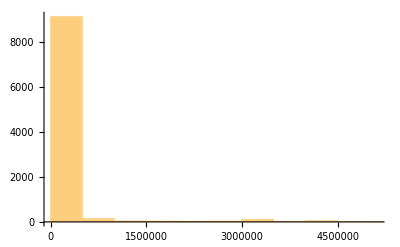

```mathematica
Length[names]
Histogram[FileByteCount/@names,50]
```

```mathematica
$ProcessID
```

81103

```mathematica
$DebugLoop=xTrue;
$visuals=xTrue;
```

```mathematica
ASTTestUtils`Private`$DebugTopLevelExpressions=xTrue;
```

```mathematica
$minSizeLimit=0.00*^6;
$maxSizeLimit=20000;
```

```mathematica
start=1;
```

```mathematica
x=start;
file=None;
Print["Parsing ", Length[names[[start;;]]]," files"];
Print["Current file: ",Dynamic[Short[file]]];
Print["Current file size: ",Dynamic[FileSize[file]]];
If[$visuals,
Print["Current file bytes/s: ",Dynamic[bytesPerSecond]]
];
Print["Current index: ",Dynamic[x]];
If[$visuals,
Print[Grid[{
{"concrete",Dynamic[AST`Library`$ConcreteParseTime],ProgressIndicator[Dynamic[AST`Library`$ConcreteParseProgress],{0,100}]},
{"aggregate",Dynamic[AST`Abstract`$AggregateParseTime],ProgressIndicator[Dynamic[AST`Abstract`$AggregateParseProgress],{0,100}]},
{"abstract",Dynamic[AST`Abstract`$AbstractParseTime],ProgressIndicator[Dynamic[AST`Abstract`$AbstractParseProgress],{0,100}]},
{"","",Dynamic[PieChart[{AST`Library`$ConcreteParseTime,AST`Abstract`$AggregateParseTime,AST`Abstract`$AbstractParseTime},ImageSize->Tiny,ChartLegends->{"concrete","aggregate","abstract"}]]}
},Alignment->Right]];
];
Print[Row[{"overall",Spacer[10],ProgressIndicator[Dynamic[x],{0,Length[names]}]}]];
Scan[(
file=#;

Which[
TrueQ[$DebugLoop],
Print[x," ",file]
,
Mod[x,100]==0,
Print[x," ",file];
NotebookSave[EvaluationNotebook[]]
];

AST`Library`$ConcreteParseProgress=Quantity[0,"Seconds"];
AST`Abstract`$AggregateParseProgress=Quantity[0,"Seconds"];
AST`Abstract`$AbstractParseProgress=Quantity[0,"Seconds"];
AST`Library`$ConcreteParseTime=Quantity[0,"Seconds"];
AST`Abstract`$AggregateParseTime=Quantity[0,"Seconds"];
AST`Abstract`$AbstractParseTime=Quantity[0,"Seconds"];
bytesPerSecond=0;
res=ASTTestUtils`parseTest[#,x,"FileNamePrefixPattern"->prefix,"FileSizeLimit"->{$minSizeLimit,$maxSizeLimit}];
(*implicitTimesTest[file,x,"FileNamePrefixPattern"->prefix];*)
If[res=!=ok,
If[$visuals,
bytesPerSecond=FileSize[file]/(AST`Library`$ConcreteParseTime);
Pause[2.0];
];
];
x++;
)&
,
names[[start;;]]
]//AbsoluteTiming
```

Parsing 9698 files

Current file:

Current file size:

Current index:

overall

100 /Users/brenton/development/stash/WA/alphasource/CalculateData/ControlledVocabulary/CVParticleAccelerator.m

200 /Users/brenton/development/stash/WA/alphasource/CalculateData/DataPaclets/BookData.m

300 /Users/brenton/development/stash/WA/alphasource/CalculateData/DataPaclets/DogBreedData.m

400 /Users/brenton/development/stash/WA/alphasource/CalculateData/DataPaclets/HistoricalCountryDataEntity.m

500 /Users/brenton/development/stash/WA/alphasource/CalculateData/DataPaclets/MusicActData.m

600 /Users/brenton/development/stash/WA/alphasource/CalculateData/DataPaclets/PolyhedronData.m

700 /Users/brenton/development/stash/WA/alphasource/CalculateData/DataPaclets/UniversityData.m

800 /Users/brenton/development/stash/WA/alphasource/CalculateData/EntityPropertyTable/BeaufortScale.m

900 /Users/brenton/development/stash/WA/alphasource/CalculateData/EntityPropertyTable/FictionalPlace.m

1000 /Users/brenton/development/stash/WA/alphasource/CalculateData/EntityPropertyTable/GrammaticalUnit.m

1100 /Users/brenton/development/stash/WA/alphasource/CalculateData/EntityPropertyTable/PaperFinish.m

1200 /Users/brenton/development/stash/WA/alphasource/CalculateData/EntityPropertyTable/StartsWithLetter.m

1300 /Users/brenton/development/stash/WA/alphasource/CalculateData/MiscellaneousData/MemeData.m

1400 /Users/brenton/development/stash/WA/alphasource/CalculateData/SupportFunctions/FlightDataFunctions.m

1500 /Users/brenton/development/stash/WA/alphasource/CalculateData/SupportFunctions/RecurringEventDataFunctions.m

1600 /Users/brenton/development/stash/WA/alphasource/CalculateExamples/Content/HealthMedicineExamples.m

1700 /Users/brenton/development/stash/WA/alphasource/CalculateFormulas/ExtraCalculators/Mathematics/Geometry/VectorCalculator.m

1800 /Users/brenton/development/stash/WA/alphasource/CalculateFormulas/Physics/Elasticity.m

1900 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalConstantData/CommonLogOfE.m

2000 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalConstantData/HardyLittlewoodPrimeQuadruplesConstant.m

2100 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalConstantData/NortonConstant.m

2200 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalConstantData/TetranacciConstant.m

2300 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionData/Csch.m

2400 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionData/HypergeometricPFQ.m

2500 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionData/Multinomial.m

2600 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionDataUpdate/AiryBiZero.m

2700 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionDataUpdate/EllipticLog.m

2800 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionDataUpdate/InverseGammaRegularized.m

2900 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionDataUpdate/MockThetaOrder3Nu.m

3000 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionDataUpdate/QBesselJ1.m

3100 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/MathematicalFunctionDataUpdate/StruveL.m

3200 /Users/brenton/development/stash/WA/alphasource/CalculateIncludes/ProbabilityDistributionData/BurrDistributionIII.m

3300 /Users/brenton/development/stash/WA/alphasource/CalculateParse/Content/AssumptionsData.m

3400 /Users/brenton/development/stash/WA/alphasource/CalculateParse/Content/FutureTopics/ReligionAndBeliefSystemsFutureTopics.m

3500 /Users/brenton/development/stash/WA/alphasource/CalculateParse/Content/Quantity.m

3600 /Users/brenton/development/stash/WA/alphasource/CalculateParse/Content/Synonyms/ParticleSynonyms.m

3700 /Users/brenton/development/stash/WA/alphasource/CalculateParse/Parser1.m

3800 /Users/brenton/development/stash/WA/alphasource/CalculateParse/Prototype/VirtualAssistant/Tests/UnitTests/VaActions/NewTask.mt

3900 /Users/brenton/development/stash/WA/alphasource/CalculateScan/ComplexAnalysisScanner.m

4000 /Users/brenton/development/stash/WA/alphasource/CalculateScan/FactorScanner.m

4100 /Users/brenton/development/stash/WA/alphasource/CalculateScan/MultiParseScanner.m

4200 /Users/brenton/development/stash/WA/alphasource/CalculateScan/PercentScanner.m

4300 /Users/brenton/development/stash/WA/alphasource/CalculateScan/SpokenResults/SRSpokenString.m

4400 /Users/brenton/development/stash/WA/alphasource/CalculateScan/TravelingScanner.m

4500 /Users/brenton/development/stash/WA/alphasource/CalculateUnits/AstronomyAndAstrophysics/Eccentricity2.m

4600 /Users/brenton/development/stash/WA/alphasource/CalculateUnits/ClassicalMechanics/GeneralizedForce.m

4700 /Users/brenton/development/stash/WA/alphasource/CalculateUnits/ClassicalMechanics/TorsionalRigidityForceTimesArea.m

4800 /Users/brenton/development/stash/WA/alphasource/CalculateUnits/Common/Diffusivity.m

4900 /Users/brenton/development/stash/WA/alphasource/CalculateUnits/Common/InverseTimeTemperatureProduct.m

5000 /Users/brenton/development/stash/WA/alphasource/CalculateUnits/Common/RadiationDose.m

$Aborted

## test Boxes from WolframLanguageData Documentation Examples

```mathematica
Quit[]
```

```mathematica
Needs["AST`"]
```

```mathematica
names=Names["System`*"];
```

```mathematica
$Debug=xTrue;
$visuals=True;
```

```mathematica
$MessagePrePrint=.
```

```mathematica
If[$visuals,
Print[Dynamic[{name,nn}]];
Print[ProgressIndicator[Dynamic[nn],{1,Length[names]}]]
]
```

```mathematica
start=1;
```

```mathematica
Get["/Users/brenton/development/stash/COD/ast/Tests/ASTTestUtils/Boxes.wl"]
```

```mathematica
Do[
nn=n;
name=names[[n]];
Which[
TrueQ[$Debug],
Print[{n,name}]
,
Mod[n,100]==0,
Print[{n,name}];
NotebookSave[EvaluationNotebook[]];
];

examples=WolframLanguageData[name,"DocumentationBasicExamples"];
Do[
If[$Debug,
Print["i: ",i];
];
example=examples[[i]];
boxes=Flatten[Cases[example,RawBoxes[Cell[BoxData[box_],___]]:>box,2]];
Do[
If[$Debug,
Print["j: ",j];
];
box=boxes[[j]];
If[$Debug&&xTrue,
Print["box: ",box//InputForm];
];
res=parseBoxTest[box,name,n,i,j];
If[res===continue,Continue[]];
If[res=!=Null,Throw[res]],
{j,1,Length[boxes]}
];
,
{i,1,Length[examples]}
]
,
{n,start,Length[names]}
]
```

{100,ψ}

$Aborted

## test Boxes from Documentation Notebooks

```mathematica
Needs["AST`"]
```

```mathematica
Get["/Users/brenton/development/stash/COD/ast/Tests/ASTTestUtils/Boxes.wl"]
```

```mathematica
names=FileNames["*.nb",$InstallationDirectory,Infinity];
```

```mathematica
Clear[descendToInputCells]
descendToInputCells[Notebook[cells_List,___]]:=descendToInputCells/@cells;
descendToInputCells[Cell[_String,_,___]]:=Null
descendToInputCells[Cell[TextData[___],_,___]]:=Null
descendToInputCells[Cell[GraphicsData[___],_,___]]:=Null
descendToInputCells[Cell[CellGroupData[cells_List,_],___]]:=descendToInputCells/@cells
descendToInputCells[Cell[BoxData[box_],"Input",___]]:=Print[parseBoxTest[box,"foo",1,2,3]]
descendToInputCells[Cell[BoxData[box_],_,___]]:=Null
descendToInputCells[args___]:=Throw[{"cannot descend",{args}}]
```

```mathematica
name=RandomChoice[names]
```

/Applications/Mathematica122-6632881.app/Contents/Documentation/English/System/ReferencePages/Symbols/Product.nb

```mathematica
NotebookOpen[name,Visible->False]
```

ggbb7_shm97FrontEndObject[LinkObject["ggbb7_shm", 3, 1]]97Product (∏)/Applications/Mathematica122-6632881.app/Contents/Documentation/English/System/ReferencePages/Symbols/Product.nb

```mathematica
nb=NotebookGet[%];
```

```mathematica
descendToInputCells[nb];
```

Null

Null

continue

Null

Null

Null

«13 more identical outputs»

continue

Null

Null

Null

«11 more identical outputs»

continue

Null

Null

Null

«6 more identical outputs»

continue

Null

Null

Null

«3 more identical outputs»

continue

Null

Null

Null

continue

continue

continue

Null

Null

Null

«5 more identical outputs»

continue

continue

Null

continue

Null

Null

continue

continue

continue

«4 more identical outputs»

Null

continue

continue

continue

«1 more identical outputs»

Null

Null

continue

Null

Null

continue

continue

continue

«2 more identical outputs»

Null

Null

continue

continue

continue

Null

Null

Null

«63 more identical outputs»

{concrete,{Length,ToStandardFormBoxes[ContainerNode[Box,{CallNode[{LeafNode[Symbol,Product,<|Source→{1,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{1,1,2}|>],InfixNode[Comma,{BinaryNode[Power,{GroupNode[GroupParen,{LeafNode[Token`OpenParen,(,<|Source→{1,1,3,1,1,1,1,1,1}|>],InfixNode[Plus,{InfixNode[Times,{LeafNode[Integer,4,<|Source→{1,1,3,1,1,1,1,1,2,1,1,1,1}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{1,1,3,1,1,1,1,1,2,1,1,1,2}|>],LeafNode[Symbol,i,<|Source→{1,1,3,1,1,1,1,1,2,1,1,1,2}|>]},<|Source→{1,1,3,1,1,1,1,1,2,1,1,1}|>],LeafNode[Token`Minus,-,<|Source→{1,1,3,1,1,1,1,1,2,1,2}|>],LeafNode[Integer,1,<|Source→{1,1,3,1,1,1,1,1,2,1,3}|>]},<|Source→{1,1,3,1,1,1,1,1,2,1}|>],LeafNode[Token`CloseParen,),<|Source→{1,1,3,1,1,1,1,1,3}|>]},<|Source→{1,1,3,1,1,1,1,1}|>],LeafNode[Token`Caret,^,<|Source→{1,1,3,1,1,1,2}|>],GroupNode[GroupParen,{LeafNode[Token`OpenParen,(,<|Source→{1,1,3,1,1,1,3,1,1}|>],InfixNode[Plus,{InfixNode[Times,{LeafNode[Integer,4,<|Source→{1,1,3,1,1,1,3,1,2,1,1,1,1}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{1,1,3,1,1,1,3,1,2,1,1,1,2}|>],LeafNode[Symbol,i,<|Source→{1,1,3,1,1,1,3,1,2,1,1,1,2}|>]},<|Source→{1,1,3,1,1,1,3,1,2,1,1,1}|>],LeafNode[Token`Minus,-,<|Source→{1,1,3,1,1,1,3,1,2,1,2}|>],LeafNode[Integer,1,<|Source→{1,1,3,1,1,1,3,1,2,1,3}|>]},<|Source→{1,1,3,1,1,1,3,1,2,1}|>],LeafNode[Token`CloseParen,),<|Source→{1,1,3,1,1,1,3,1,3}|>]},<|Source→{1,1,3,1,1,1,3,1}|>]},<|Source→{1,1,3,1,1,1}|>],LeafNode[Token`Comma,,,<|Source→{1,1,3,1,2}|>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<|Source→{1,1,3,1,3,1,1}|>],InfixNode[Comma,{LeafNode[Symbol,i,<|Source→{1,1,3,1,3,1,2,1,1}|>],LeafNode[Token`Comma,,,<|Source→{1,1,3,1,3,1,2,1,2}|>],LeafNode[Symbol,n,<|Source→{1,1,3,1,3,1,2,1,3}|>]},<|Source→{1,1,3,1,3,1,2,1}|>],LeafNode[Token`CloseCurly,},<|Source→{1,1,3,1,3,1,3}|>]},<|Source→{1,1,3,1,3,1}|>]},<|Source→{1,1,3,1}|>],LeafNode[Token`CloseSquare,],<|Source→{1,1,4}|>]},<||>]},<|Source→{1,1}|>],LeafNode[Token`Newline,
,<|Source→{2}|>]},<||>]]},{foo,1,2,3}}

Null

continue

from boxes:  {BinaryNode[BinarySlashSlash,{CallNode[LeafNode[Symbol,Grid,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,Join,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,f,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,k,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Text,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[String,"Infinite Product",<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Transpose,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,flist,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Token`SemiSemi,;;,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Map,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{PostfixNode[Function,{CallNode[LeafNode[Symbol,Product,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,1,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,k,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,2,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,3,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Amp,&,<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Symbol,flist,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Background,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,GrayLevel,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Real,.9,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,2,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,BaseStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{LeafNode[Symbol,FontFamily,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,Times,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FontSize,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Integer,12,<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Dividers,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,All,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FrameStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.8,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Spacings,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,2,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`SlashSlash,//,<||>],LeafNode[Symbol,TraditionalForm,<||>]},<||>]}
from string: {BinaryNode[BinarySlashSlash,{CallNode[LeafNode[Symbol,Grid,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,Join,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,f,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,k,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Text,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[String,"Infinite Product",<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Transpose,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{CallNode[LeafNode[Symbol,flist,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{BinaryNode[Span,{LeafNode[Token`Fake`ImplicitOne,,<||>],LeafNode[Token`SemiSemi,;;,<||>],LeafNode[Token`Fake`ImplicitAll,,<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,Map,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{PostfixNode[Function,{CallNode[LeafNode[Symbol,Product,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,1,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,k,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,2,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Slot,#,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Integer,3,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Amp,&,<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Symbol,flist,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Background,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Symbol,None,<||>],LeafNode[Token`Comma,,,<||>],CallNode[LeafNode[Symbol,GrayLevel,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Real,.9,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,1,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,2,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,BaseStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{BinaryNode[Rule,{LeafNode[Symbol,FontFamily,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,Times,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FontSize,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Integer,12,<||>]},<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Dividers,<||>],LeafNode[Token`LongName`Rule,→,<||>],LeafNode[Symbol,All,<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,FrameStyle,<||>],LeafNode[Token`LongName`Rule,→,<||>],CallNode[LeafNode[Symbol,Hue,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{LeafNode[Real,.6,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.4,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Real,.8,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Comma,,,<||>],BinaryNode[Rule,{LeafNode[Symbol,Spacings,<||>],LeafNode[Token`LongName`Rule,→,<||>],GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],InfixNode[Comma,{LeafNode[Integer,2,<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Integer,1,<||>]},<||>],LeafNode[Token`CloseCurly,},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`SlashSlash,//,<||>],LeafNode[Symbol,TraditionalForm,<||>]},<||>]}

{comparing aggs,foo,1,2,3}

## random string testing

```mathematica
Needs["AST`"]
```

```mathematica
$ProcessID
```

18523

```mathematica
get=Get["/Users/brenton/development/stash/COD/ast/tables/LongNames.wl"];
```

```mathematica
punct=Select[get,#==PunctuationCharacter&];
```

```mathematica
raw=Select[get,#==RawCharacter&];
```

```mathematica
unsupported=Select[get,#==UnsupportedCharacter&];
```

```mathematica
punctNames=Keys[punct];
```

```mathematica
rawNames=Keys[raw];
```

```mathematica
unsupportedNames=Keys[unsupported];
```

```mathematica
names=punctNames;
```

```mathematica
names=Complement[names,rawNames];
```

```mathematica
names=Complement[names,unsupportedNames];
```

```mathematica
dontBother={"InvisibleComma","Integral","ContourIntegral","DoubleContourIntegral","ClockwiseContourIntegral","CounterClockwiseContourIntegral"};
names=Complement[names,dontBother];
```

```mathematica
buggy={"ImplicitPlus",
"Star",
"Coproduct",
"LeftDoubleBracket",
"DiscretionaryParagraphSeparator",
"DiscretionaryLineSeparator"};
buggy={};
```

```mathematica
parseToSymbols={"Infinity",
"ImaginaryI",
"Pi",
"ImaginaryJ",
"Degree",
"ExponentialE"};
parseToSymbols={};
```

```mathematica
names=Complement[names,buggy];
```

```mathematica
names=Complement[names,parseToSymbols];
```

```mathematica
names//Length
```

298

```mathematica
tabProb=0;
newlineProb=0;
spaceProb=0;
punctProb=0;
```

```mathematica
rules=Rule@@Transpose[{{tabProb,"\t"},{newlineProb,"\n"},{0," "},{0,"!"},{0,"\""},{0,"#"},{0,"$"},{0,"%"},{0,"&"},{0,"'"},{0,"("},{0,")"},{1,"*"},{1,"+"},{0,","},{1,"-"},{1,"."},{0,"/"},{1,"1"},{2,"1"},{3,"1"},
{0,":"},{0,";"},{0,"<"},{0,"="},{0,">"},{0,"?"},{0,"@"},
{0,"A"},
{0,"["},
{0,"\\"},
{0,"]"},
{1,"^"},
{0,"_"},{1,"`"},{0,"{"},{0,"|"},{0,"}"},{0,"~"}}~Join~(({0,"\\["<>#<>"]"})&/@names)];
```

### test

```mathematica
$ProcessID
```

18523

bug 382766: a . -b cannot be parsed
bug 385771: Inequality (Greater, Less, etc.) operators are absorbed by VectorInequality operators
bug 385777: Parsing \ [Star] and implicit Times is buggy
bug 385784: Context (with no symbol) is silently truncated from RHS of _
bug 365287: ImplicitPlus

```mathematica
bothFailed=0;
bothSucceeded=0;
bug385771=0;
bug385777=0;
bug382766=0;
bug385784=0;
stringification=0;
bug365287=0;
toReport1=0;
toReport2=0;
bad=0;
badStrs={};
```

```mathematica
Print[Grid[{
{"bothFailed",Dynamic[bothFailed]},
{"bothSucceeded",Dynamic[bothSucceeded]},
{"bug385771",Dynamic[bug385771]},
{"bug385777",Dynamic[bug385777]},
{"bug382766",Dynamic[bug382766]},
{"bug385784",Dynamic[bug385784]},
{"stringification",Dynamic[stringification]},
{"bug365287",Dynamic[bug365287]},
{"toReport1",Dynamic[toReport1]},
{"toReport2",Dynamic[toReport2]},
{"bad",Dynamic[bad]},
{"","",Dynamic[PieChart[{Log[bothFailed],Log[bothSucceeded],Log[bug385771],Log[bug385777],Log[bug382766],Log[bug385784],Log[stringification],Log[bug365287],Log[toReport1],Log[toReport2],Log[bad]},ImageSize->Tiny,ChartLegends->{"bothFailed","bothSucceeded","bug385771","bug385777","bug382766","bug385784","stringification","bug365287","toReport1","toReport2","bad"}]]}
},Alignment->Right]]
```

bothFailed |  | 
bothSucceeded |  | 
bug385771 |  | 
bug385777 |  | 
bug382766 |  | 
bug385784 |  | 
stringification |  | 
bug365287 |  | 
toReport1 |  | 
toReport2 |  | 
bad |  | 
 |  |

```mathematica
Print[Dynamic[str]]
```

```mathematica
While[True,
Pause[0.0];

str=StringJoin[RandomChoice[rules,15]];

str >> "/Users/brenton/development/stash/COD/ast/build/test.m";

expr=Quiet[ToExpression[str,InputForm,Hold]];

If[expr===$Failed,

test=ParseString[str,ContainerNode[Hold,#[[1]],<||>]&];

(*If[!FreeQ[test,CallNode[LeafNode[Symbol,"Dot",_],{___,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus"|"Not"|"Span",_],_,_]|
PrefixNode[Minus,{LeafNode[Token`Minus,"-",_],_},_]},_]|
CallNode[LeafNode[Symbol,"Put"|"Get",_],_,_]],Continue[]];*)

testStr=ToFullFormString[test];

If[StringQ[testStr],
If[!StringFreeQ[testStr,"AST`Comma"],
comma++;
testStr=Failure["CommaFailure",<||>];
];
];

If[!FailureQ[testStr],

If[!FreeQ[test,CallNode[LeafNode[Symbol,"Dot",_],{___,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus"|"Not"|"Span",_],_,_]|
PrefixNode[Minus|PreIncrement,_,_]|
LeafNode[Real|Integer,s_/;StringStartsQ[s,"-"],_]},_]],bug382766++;Continue[]];

If[!FreeQ[test,CallNode[LeafNode[Symbol,"Put"|"Get",_],_,_]],stringification++;Continue[]];

If[!FreeQ[test,PostfixNode[Repeated,{LeafNode[Integer,s_/;StringContainsQ[s,"^^"],_],LeafNode[Token`DotDot,"..",_]},_]],
toReport2++;Continue[]
];

xPrint["ToExpression failed; CodeTools succeeded"];
fullFormStr=$Failed;

bad++;
AppendTo[badStrs,str];

Continue[]
];

bothFailed++;
Continue[]
];

If[!FreeQ[expr,Information,Infinity,Heads->True],
information++;
Continue[]
];

(*If[!FreeQ[expr,_Real,Infinity,Heads->True],Continue[]];*)

(*If[!FreeQ[expr,Get|MessageName|Put|PutAppend,Infinity,Heads->True],Continue[]];*)

(*If[!FreeQ[expr,Null,Infinity,Heads->True],Continue[]];*)

fullFormStr=ToString[FullForm[expr]];

(*If[!StringFreeQ[fullFormStr,"\\\\"],Continue[]];*)

If[!StringFreeQ[fullFormStr,"Developer`VectorInequality"],bug385771++;Continue[]];

test=ParseString[str,ContainerNode[Hold,#[[1]],<||>]&];

(*If[!FreeQ[test,(*CallNode[LeafNode[Symbol,"Dot",_],{_,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus",_],_,_]|
PrefixNode[Minus,{LeafNode[Token`Minus,"-",_],_},_]|
CallNode[LeafNode[Symbol,"Not",_],_,_]},_]|*)
LeafNode[Token`QuestionQuestion,"??",_]],Continue[]];*)

(*
reals can print differently:
.8 vs. 0.8, etc.

symbols can print differently:
`a vs. a

integers can print differently: 0123
*)
testStr=ToFullFormString[test/.{
LeafNode[Real,r_,data_]:>LeafNode[Real,ToString[FullForm[ToExpression[r]]],data],
LeafNode[Integer,i_,data_]:>LeafNode[Integer,ToString[FullForm[ToExpression[i]]],data],
LeafNode[Symbol,s_,data_]:>LeafNode[Symbol,ToExpression[s,InputForm,Function[xx,ToString[Unevaluated[xx],InputForm],{HoldFirst}]],data]}];

If[FailureQ[testStr],

cst=ConcreteParseString[str];

If[!FreeQ[cst,
PatternBlankNode[PatternBlank,{_,_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]|
BlankNode[Blank,{_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]|
BlankSequenceNode[BlankSequence,{_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]],
bug385784++;
Continue[]
];

If[!FreeQ[cst,
InfixNode[Plus,{
LeafNode[Real,s_/;StringMatchQ[s,___~~"`"],_]|InfixNode[Times,{___,LeafNode[Real,s_/;StringMatchQ[s,___~~"`"],_]},_]
,
LeafNode[Token`Minus|Token`Plus,_,_],InfixNode[Times,{ErrorNode[Token`Error`ExpectedOperand,_,_],LeafNode[Token`Star,"*",_],___},_]},_]],
toReport1++;
Continue[]
];

xPrint["ToExpression succeeded; CodeTools failed"];

bad++;
AppendTo[badStrs,str];

Continue[]
];

(*If[!StringFreeQ[testStr,"\\<"|"\\>"|"\\ "],Continue[]];*)

If[testStr=!=fullFormStr,

cst=ConcreteParseString[str];

If[!FreeQ[cst,InfixNode[Star,{___,InfixNode[Times,{___,LeafNode[Token`Fake`ImplicitTimes,_,_],___},_],___},_]],
bug385777++;
Continue[]
];

If[!FreeQ[cst,LeafNode[Token`LongName`ImplicitPlus,_,_]],
bug365287++;
Continue[]
];

xPrint["exprs succeeded, but differ"];

bad++;
AppendTo[badStrs,str];

Continue[];
];

bothSucceeded++;
]
```

$Aborted

### examine

```mathematica
badStrs
```

{1`*1111`1*11^^.}

```mathematica
1-*2
```

```mathematica
11
```

11

```mathematica
Quit[]
```

```mathematica
1
```

1

```mathematica
ToExpression["2^^.",InputForm,Hold]//FullForm
```

$Failed

```mathematica
ConcreteParseString["2^^."]
```

ContainerNode[String,{LeafNode[Real,2^^.,<|Source→{{1,1},{1,5}}|>]},<||>]

```mathematica
ParseString[".1`+*1"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,Plus,<||>],{LeafNode[Real,.1`,<|Source→{{1,1},{1,4}}|>],CallNode[LeafNode[Symbol,Times,<||>],{ErrorNode[Token`Error`ExpectedOperand,,<|Source→{{1,4},{1,4}}|>],LeafNode[Integer,1,<|Source→{{1,6},{1,7}}|>]},<|Source→{{1,4},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>]},<|SyntaxIssues→{FormatIssue[Space,Suspicious syntax.,Formatting,<|Source→{{1,4},{1,4}},Format`AirynessLevel→0.25,CodeActions→{CodeAction[Insert space,InsertText,<|Source→{{1,4},{1,4}},InsertionText→ |>]}|>]}|>]

Failure[…]

```mathematica
str
```

A_*-A_1_  -\[DifferentialD]!_1

```mathematica
test/.LeafNode[Real,_,_]->LeafNode[Symbol,"$real",<||>]
```

ContainerNode[Hold,{CallNode[LeafNode[Symbol,Plus,<||>],{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Pattern,<||>],{LeafNode[Symbol,A,<|Source→{{1,1},{1,2}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<||>]},<|Source→{{1,1},{1,3}}|>],LeafNode[Integer,-1,<||>],CallNode[LeafNode[Symbol,Pattern,<||>],{LeafNode[Symbol,A,<|Source→{{1,5},{1,6}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<||>]},<|Source→{{1,5},{1,7}}|>],LeafNode[Integer,1,<|Source→{{1,7},{1,8}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<|Source→{{1,8},{1,9}}|>]},<|Source→{{1,1},{1,9}}|>],CallNode[LeafNode[Symbol,Times,<||>],{LeafNode[Integer,-1,<||>],CallNode[LeafNode[Symbol,DifferentialD,<||>],{CallNode[LeafNode[Symbol,Not,<||>],{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Blank,<||>],{},<|Source→{{1,29},{1,30}}|>],LeafNode[Integer,1,<|Source→{{1,30},{1,31}}|>]},<|Source→{{1,29},{1,31}}|>]},<|Source→{{1,28},{1,31}}|>]},<|Source→{{1,12},{1,31}}|>]},<|Source→{{1,11},{1,31}}|>]},<|Source→{{1,1},{1,31}}|>]},<||>]

```mathematica
testStr
```

Hold[Plus[Times[Pattern[A, Blank[]], -1, Pattern[A, Blank[]], 1, Blank[]], Times[-1, DifferentialD[Not[Times[Blank[], 1]]]]]]

```mathematica
expr//FullForm
```

$Failed

```mathematica
fullFormStr
```

Hold[Set[Plus[Times[A1, Power[Blank[$], -1]], -1, -1.`], BlankSequence[]]]

```mathematica
ParseString["%a"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Out,<||>],{},<|Source→{{1,1},{1,2}}|>],LeafNode[Symbol,a,<|Source→{{1,2},{1,3}}|>]},<|Source→{{1,1},{1,3}}|>]},<||>]

Times[Out[], a]

```mathematica
ToExpression["\\[CapitalDifferentialD]",InputForm,Hold]//FullForm
```

ToExpression::sntx: Invalid syntax in or before " ".
                                                 ^

$Failed

```mathematica
ToExpression["a \\[Star] b * c",InputForm,Hold]//FullForm
```

Hold[Star[a,Times[b,c]]]

```mathematica
ParseString["\\[CapitalDifferentialD] ! a"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,CapitalDifferentialD,<||>],{CallNode[LeafNode[Symbol,Not,<||>],{LeafNode[Symbol,a,<|Source→{{1,27},{1,28}}|>]},<|Source→{{1,25},{1,28}}|>]},<|Source→{{1,1},{1,28}}|>]},<||>]

CapitalDifferentialD[Not[a]]

```mathematica
ToExpression["\\[CapitalDifferentialD] ! a",InputForm,Hold]//FullForm
```

ToExpression::sntx: Invalid syntax in or before "ⅅ ! a".
                                                                          ^

$Failed

```mathematica
ConcreteParseString["\\[CapitalDifferentialD]"]
```

ContainerNode[String,{PrefixNode[CapitalDifferentialD,{LeafNode[Token`LongName`CapitalDifferentialD,\[CapitalDifferentialD],<|Source→{{1,1},{1,24}}|>],LeafNode[Token`Error`ExpectedOperand,,<|Source→{{1,24},{1,24}}|>]},<|Source→{{1,1},{1,24}}|>]},<||>]

```mathematica
InfixNode[Star,{___,InfixNode[Times,{___,LeafNode[Token`Fake`ImplicitTimes,_,_],___},_],___},_]
```

```mathematica
ToExpression["a . !b"]
```

ToExpression::sntx: Invalid syntax in or before "a . !b".
                                                      ^

$Failed

```mathematica
x=1
```

1

```mathematica
ToExpression["`x",InputForm,Function[xx,ToString[Unevaluated[xx],InputForm],{HoldFirst}]]
```

x

```mathematica
ParseString["56`"]
ToFullFormString[%]
```

ContainerNode[String,{LeafNode[Real,56`,<|Source→{{1,1},{1,4}}|>]},<||>]

56`

```mathematica
ToString[ToExpression[56],InputForm]
```

56.

```mathematica
ToString[FullForm[56.]]
```

56.`

```mathematica
Needs["AST`"]
```

```mathematica
ConcreteParseString["1XD\\[NotLessLess]_`6COUGcb$%"]
```

ContainerNode[String,{InfixNode[Inequality,{InfixNode[Times,{LeafNode[Integer,1,<|Source→{{1,1},{1,2}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,2},{1,2}}|>],LeafNode[Symbol,XD,<|Source→{{1,2},{1,4}}|>]},<|Source→{{1,1},{1,4}}|>],LeafNode[Token`LongName`NotLessLess,\[NotLessLess],<|Source→{{1,4},{1,18}}|>],InfixNode[Times,{BlankNode[Blank,{LeafNode[Blank,_,<|Source→{{1,18},{1,19}}|>],LeafNode[Token`Error`ExpectedLetterlike,`6,<|Source→{{1,19},{1,21}}|>]},<|Source→{{1,18},{1,21}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,21},{1,21}}|>],LeafNode[Symbol,COUGcb$,<|Source→{{1,21},{1,28}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,28},{1,28}}|>],LeafNode[Out,%,<|Source→{{1,28},{1,29}}|>]},<|Source→{{1,18},{1,29}}|>]},<|Source→{{1,1},{1,29}}|>]},<||>]

```mathematica
ConcreteParseString["_Foo`"]
```

ContainerNode[String,{LeafNode[Blank,_,<|Source→{{1,1},{1,2}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,2},{1,6}}|>]},<||>]

```mathematica
ConcreteParseString["a_Foo`"]
```

ContainerNode[String,{PatternBlankNode[PatternBlank,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Blank,_,<|Source→{{1,2},{1,3}}|>]},<|Source→{{1,1},{1,3}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,3},{1,7}}|>]},<||>]

```mathematica
ConcreteParseString["a_Foo`"]
```

ContainerNode[String,{PatternBlankNode[PatternBlank,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Blank,_,<|Source→{{1,2},{1,3}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,3},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>]},<||>]

```mathematica
ToExpression["∯ a! ∃ b",InputForm,Hold]//FullForm
```

Hold[Times[DoubleContourIntegral[Factorial[a]],Exists[b]]]

```mathematica
ParseString["∯ a! ∃ b"];
ToFullFormString[%]
```

DoubleContourIntegral[Times[Factorial[a], Exists[b]]]

```mathematica
ConcreteParseString["a \\[ImplicitPlus] "]
```

ContainerNode[String,{InfixNode[Plus,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Whitespace, ,<|Source→{{1,2},{1,3}}|>],LeafNode[Token`LongName`ImplicitPlus,\[ImplicitPlus],<|Source→{{1,3},{1,18}}|>],LeafNode[Token`Error`ExpectedOperand,,<|Source→{{1,18},{1,18}}|>]},<|Source→{{1,1},{1,18}}|>],LeafNode[Whitespace, ,<|Source→{{1,18},{1,19}}|>]},<||>]

```mathematica
ConcreteParseString["`A1/_$-1-1`=__`"]
```

ContainerNode[String,{BinaryNode[Set,{InfixNode[Plus,{BinaryNode[Divide,{LeafNode[Symbol,`A1,<|Source→{{1,1},{1,4}}|>],LeafNode[Token`Slash,/,<|Source→{{1,4},{1,5}}|>],BlankNode[Blank,{LeafNode[Blank,_,<|Source→{{1,5},{1,6}}|>],LeafNode[Symbol,$,<|Source→{{1,6},{1,7}}|>]},<|Source→{{1,5},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>],LeafNode[Token`Minus,-,<|Source→{{1,7},{1,8}}|>],LeafNode[Integer,1,<|Source→{{1,8},{1,9}}|>],LeafNode[Token`Minus,-,<|Source→{{1,9},{1,10}}|>],LeafNode[Real,1`,<|Source→{{1,10},{1,12}}|>]},<|Source→{{1,1},{1,12}}|>],LeafNode[Token`Equal,=,<|Source→{{1,12},{1,13}}|>],BlankSequenceNode[BlankSequence,{LeafNode[BlankSequence,__,<|Source→{{1,13},{1,15}}|>],LeafNode[Token`Error`ExpectedLetterlike,`,<|Source→{{1,15},{1,16}}|>]},<|Source→{{1,13},{1,16}}|>]},<|Source→{{1,1},{1,16}}|>]},<||>]

```mathematica
ConcreteParseString[]
```

```mathematica
badStrs[[1]]
```

\[CapitalDifferentialD]!A1|11A ^11A:A